## EquationTrekker

```mathematica
Needs["EquationTrekker`"]
```

icon | mode |  
 | select treks mode | Mouse button selects treks. Multiple treks may be selected by dragging or using Shift+click. Once treks are selected, you may
• Delete them by using the Del key.
• Move their starting position(s) by dragging.
• Change their color using the color well tool .
Ctrl+click or right-click creates treks. Dragging allows you to interactively change the position of the newly created trek.
 | create treks mode | Mouse button creates new treks.
Ctrl+click or right-click selects treks.
Dragging the create treks button opens a menu that allows you to toggle the default drawing mode between lines and points. The last item on the toolbar indicates the current drawing mode.
 | zoom mode | In zoom mode,
• Dragging the mouse shows a rectangle which will become the new range. The default behavior is to use a rectangle which preserves the aspect ratio of the current graph. Pressing the Ctrl key while dragging changes to a rectangle which can change the aspect ratio.
• Shift+drag shows a rectangle that the edges of the current plot region will be mapped to (zoom out).
• Ctrl+drag (right drag) pans.
Dragging the Zoom Mode button opens a menu which allows you to select zoom to fit or scale to fit. Zoom to fit finds a plot range in which all the trajectories fit, preserving aspect ratio. Scale to fit finds the smallest plot range in which all the trajectories fit.
 | pan mode | Mouse button pans selected point to center. Dragging pans interactively.
Right-click or Ctrl+click zooms.

### Ejemplo clave

```mathematica
NDSolve[{x''[t]+1/10x'[t]+Sin[x[t]]==1/2 Cos[t],x[0]==x'[0]==0},x,{t,0,100}]
```

{{x→InterpolatingFunction[{{0.,100.}},<>]}}

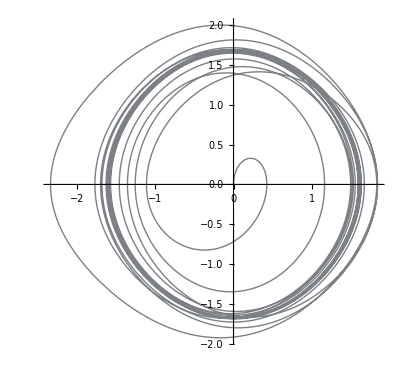

```mathematica
ParametricPlot[Evaluate[{x[t],x'[t]}/.%],{t,0,100},ColorFunction->Hue]
```

### Ejemplo 01

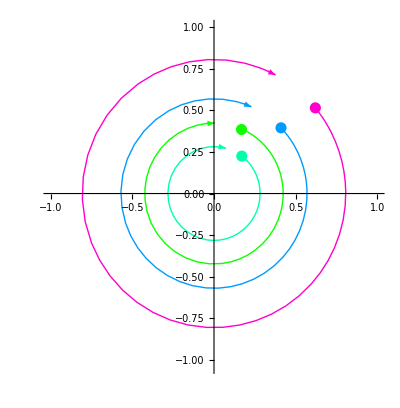
{EquationTrekkerState["xyxπ/82","{}",TrekData["0.39269908169872414y'", <>]
TrekData["0.39269908169872414y'", <>]
TrekData["0.39269908169872414y'", <>]
TrekData["0.39269908169872414y'", <>], <>],-Graphics-}

```mathematica
EquationTrekker[y''[x] + y[x] == 0,y,{x,π/8, 2 π}]
```

### Ejemplo 02

NDSolve`Iterate::ndsz: At t == 1.08174, step size is effectively zero; singularity or stiff system suspected.

NDSolve`Iterate::ndsz: At t == 1.60772, step size is effectively zero; singularity or stiff system suspected.

NDSolve`Iterate::ndsz: At t == 2.20872, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve`Iterate :: ndsz will be suppressed during this calculation.

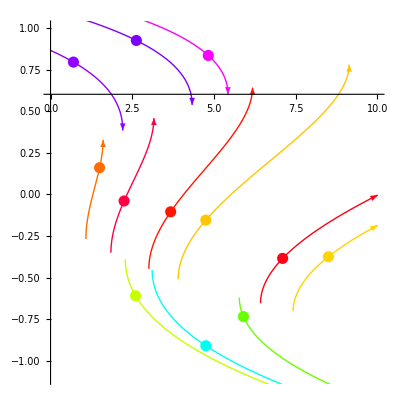
{EquationTrekkerState["1/(-t + 15 SuperscriptBox[z[t], 2])zt010","{}",TrekData["z[4.825] == 0.835", <>]
TrekData["z[5.9] == -0.735", <>]
TrekData["z[4.75] == -0.91", <>]
TrekData["z[7.1] == -0.385", <>]
TrekData["z[3.675] == -0.105", <>]
TrekData["z[2.25] == -0.04", <>]
TrekData["z[2.625] == 0.925", <>]
TrekData["z[8.5] == -0.375", <>]
TrekData["z[4.75] == -0.155", <>]
TrekData["z[2.6] == -0.61", <>]
TrekData["z[0.7] == 0.795", <>]
TrekData["z[1.5] == 0.16", <>], <>],-Graphics-}

```mathematica
EquationTrekker[z'[t]  +1/(15 z[t]^2  - t)  ==0, z, {t,0,10}]
```

### Ejemplo 03

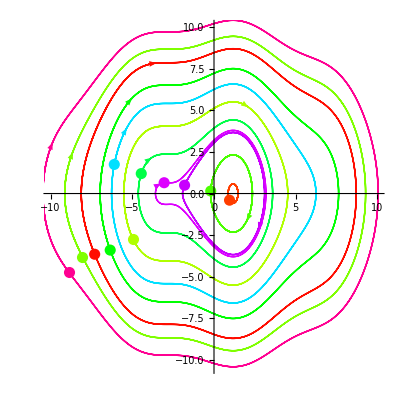
{EquationTrekkerState["txt-1010","{α → 3., ω → 1.}",TrekData["-10.x'", <>]
TrekData["-10.x'", <>]
TrekData["-10.x'", <>]
TrekData["-10.x'", <>]
TrekData["-10.x'", <>]
TrekData["-10.x'", <>]
TrekData["-10.x'", <>]
TrekData["-10.x'", <>]
TrekData["-10.x'", <>]
TrekData["-10.x'", <>]
TrekData["-10.x'", <>], <>],-Graphics-}

```mathematica
EquationTrekker[x''[t] + x[t] == α Cos[ω x[t]],x,{t,-10,10}, PlotRange->{{-10,10},{-10,10}},TrekParameters->{α->3, ω->1}]
```

### Ejemplo 04

```mathematica
EquationTrekker[x''[t] + x[t] == α Cos[ω x[t]],x,{t,-10,10}, PlotRange->{{-4,4},{-4,4}},TrekParameters->{α->3,  ω->{1,{0,20}}}]
```

{EquationTrekkerState["txt-1010","{α → 3., ω → 1.}",{}, <>],{}}

### Ejemplo 05

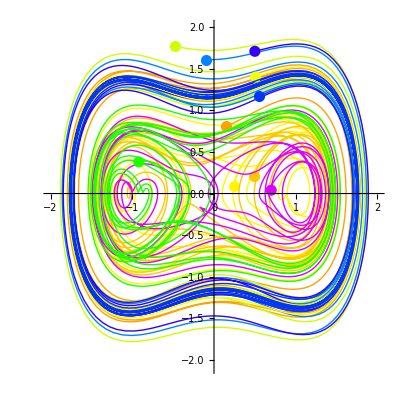
{EquationTrekkerState["-x[t]xt0100","{γ → 0.15, ϵ → 0.3, ω → 1.}",TrekData["0.x'", <>]
TrekData["0.x'", <>]
TrekData["0.x'", <>]
TrekData["0.x'", <>]
TrekData["0.x'", <>]
TrekData["0.x'", <>]
TrekData["0.x'", <>]
TrekData["0.x'", <>]
TrekData["0.x'", <>]
TrekData["0.x'", <>], <>],-Graphics-}

```mathematica
EquationTrekker[{ x''[t] + γ x'[ t] - x[t] + x[t]^3 == ϵ Cos[ω t]}, x, {t,0,100},
PlotRange->{{-2,2},{-2,2}},
TrekParameters->{γ->.15, ϵ->.3, ω->1.}]
```

### Ejemplo 06

```mathematica
EquationTrekker[{ x''[t] + γ x'[ t] - x[t] + x[t]^3 == ϵ Cos[ω t]}, x, {t,1000, 10000},
PlotRange->{{-2,2},{-2,2}},
TrekParameters->{γ->.15, ϵ->.3, ω->1.}, TrekGenerator->{PoincareSection, "SectionCondition"->Mod[ω t, 2 π], "SectionVariables"->{x, x'},MaxSteps->∞}]
```

### Ejemplo 07

```mathematica
NDSolve[{x'[t]==-3 (x[t]-y[t]),y'[t]==-x[t] z[t]+26.5 x[t]-y[t],z'[t]==x[t] y[t]-z[t],x[0]==z[0]==0,y[0]==1},{x,y,z},{t,0,200},MaxSteps->Infinity]
```

{{x→InterpolatingFunction[{{0.,200.}},<>],y→InterpolatingFunction[{{0.,200.}},<>],z→InterpolatingFunction[{{0.,200.}},<>]}}

```mathematica
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.%],{t,0,200},PlotPoints->10000,ColorFunction->(ColorData["Rainbow"][#4]&)]
```

-Graphics3D-

### Ejemplo 08

```mathematica
NDSolve[{D[u[t,x],t,t]==D[u[t,x],x,x]+(1-u[t,x]^2)(1+2u[t,x]),u[0,x]==Exp[-x^2],Derivative[1,0][u][0,x]==0,u[t,-10]==u[t,10]},u,{t,0,10},{x,-10,10}]
```

{{u→InterpolatingFunction[{{0.,10.},{-10.,10.}},<>]}}

```mathematica
Plot3D[Evaluate[u[t,x]/.First[%]],{t,0,6},{x,-6,6},PlotPoints->100]
```

-Graphics3D-

```mathematica
DensityPlot[Evaluate[u[10-t,x]/.First[%%]],{x,-10,10},{t,0,10},PlotPoints->200,Mesh->False]
```

-Graphics-

```mathematica
eqn=D[u[t,x,y],t,t]==D[u[t,x,y],x,x]+D[u[t,x,y],y,y]/2+(1-u[t,x,y]^2)(1+2u[t,x,y])
```

u^(2,0,0)[t,x,y]==(1+2 u[t,x,y]) (1-u[t,x,y]^2)+1/2 u^(0,0,2)[t,x,y]+u^(0,2,0)[t,x,y]

```mathematica
NDSolve[{eqn,u[0,x,y]==Exp[-(x^2+y^2)],u[t,-5,y]==u[t,5,y],u[t,x,-5]==u[t,x,5],Derivative[1,0,0][u][0,x,y]==0},u,{t,0,4},{x,-5,5},{y,-5,5}]
```

{{u→InterpolatingFunction[{{0.,4.},{-5.,5.},{-5.,5.}},<>]}}

```mathematica
Table[Plot3D[Evaluate[u[t,x,y]/.First[%]],{x,-5,5},{y,-5,5},PlotRange->All,PlotPoints->100,Mesh->False],{t,1,4}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}